# Rosenzweig-MacArthur Predator-Prey

The Rosenzweig-MacArthur predator-prey model combines logistic growth of prey (n) and predators (p) who have a type-II functional response.  It can exhibit either equilibrium behavior or a predator-prey limit cycle at high prey carrying capacity.

```mathematica
Needs["EcoEvo`"];
```

Set up the model:

```mathematica
SetModel[{
Pop[n]->{Equation:>n[t]*(1-n[t]/k)-a p[t]n[t]/(n[t]+h),Color->Green},
Pop[p]->{Equation:>p[t]*(b n[t]/(n[t]+h)-m),Color->Red},Assumptions->{a>0,b>0,h>0,m>0,k>0,b>m}
}];
```

Solve for equilibria:

```mathematica
eq=SolveEcoEq[]
```

{{n→0,p→0},{n→k,p→0},{n→(h m)/(b-m),p→(b h (b k-h m-k m))/(a k (b-m)^2)}}

Check the linear stability of each equilibrium:

```mathematica
Simplify[EcoStableQ[eq]]
```

{False,Piecewise[{{True, b k<(h+k) m}, {False, b k>(h+k) m}, {Indeterminate, True}}],Piecewise[{{True, b h+(h+k) m>b k&&b k>(h+k) m}, {False, b k<(h+k) m||b h+(h+k) m<b k}, {Indeterminate, True}}]}

Note that the stability condition for the predator-prey coexistence equilibrium was determined using RouthHurwitzCriteria.

```mathematica
Simplify[RouthHurwitzCriteria[EcoJacobian[eq⟦-1⟧]]]
```

Piecewise[{{True, b h+(h+k) m>b k&&(h+k) m<b k}, {False, b h+(h+k) m<b k||(h+k) m>b k}, {Indeterminate, True}}]

Let's rearrange the stability conditions of the coexistence equilibrium in terms of k.  The second is a transcritical bifurcation where the predator comes into existence, the first is a Hopf bifurcation where a predator-prey limit cycle is born.

```mathematica
kpred=k/.Solve[b k==(h+k) m,k]⟦1⟧
```

(h m)/(b-m)

```mathematica
khopf=Simplify[k/.Solve[b h+(h+k) m==b k,k]⟦1⟧]
```

(h (b+m))/(b-m)

Calculate the rate predators invade the prey-only equilibrium:

```mathematica
Inv[eq⟦2⟧,p]
```

(b k)/(h+k)-m

Setting this equal to zero gives the same critical value for predator invasion as above:

```mathematica
Solve[Inv[eq⟦2⟧,p]==0,k]
```

{{k→(h m)/(b-m)}}

To summarize the possible outcomes:

0 < k < (h m)/(b-m) | only prey
 (h m)/(b-m) < k < h(b+m)/(b-m) | stable predator-prey coexistence
k> h(b+m)/(b-m) | unstable predator-prey coexistence (limit cycle)

Let's plot phase planes and simulate the model for all of these cases.  First, define parameter values and calculate the critical k values.

```mathematica
a=1;b=2;h=1;m=1;
{kpred,khopf}
```

{1,3}

### Case I - Only Prey (k<1)

```mathematica
k=0.5;
```

```mathematica
eq
```

{{n→0,p→0},{n→0.5,p→0},{n→1,p→-2.}}

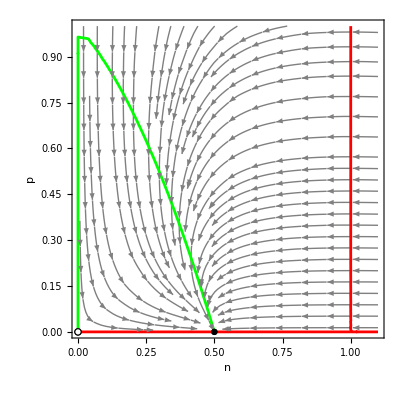

```mathematica
Show[
PlotEcoPhasePlane[{n,0,1.1},{p,0,1}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
```

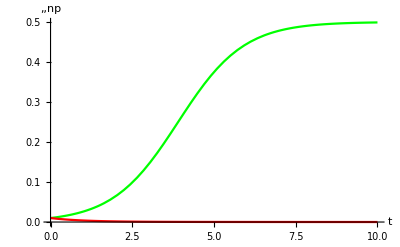

```mathematica
sol=EcoSim[{n->0.01,p->0.01},10];
PlotDynamics[sol]
```

### Case II - Stable Predator-Prey Coexistence (1<k<3)

```mathematica
k=2;
```

```mathematica
eq
```

{{n→0,p→0},{n→2,p→0},{n→1,p→1}}

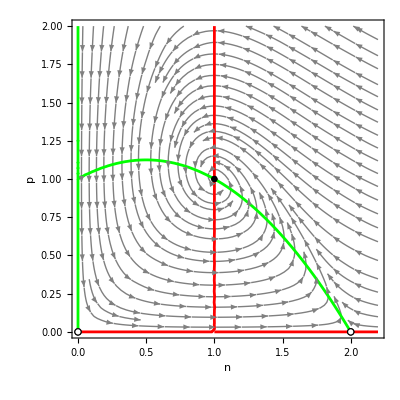

```mathematica
Show[
PlotEcoPhasePlane[{n,0,2.2},{p,0,2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
```

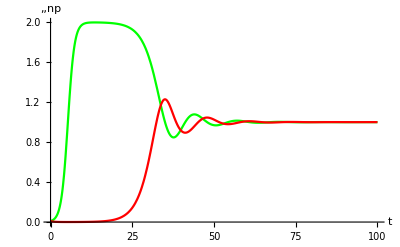

```mathematica
sol=EcoSim[{n->0.01,p->0.01},100];
PlotDynamics[sol]
```

### Case III - Unstable Predator-Prey Coexistence (k>3)

```mathematica
k=4;
```

```mathematica
eq
```

{{n→0,p→0},{n→4,p→0},{n→1,p→3/2}}

Calculate eigenvalues of the predator-prey equilibrium to verify its instability:

```mathematica
N[EcoEigenvalues[eq⟦-1⟧]]
```

{0.0625+0.609175 ⅈ,0.0625-0.609175 ⅈ}

The positive real part indicates instability and the imaginary part indicates oscillations.

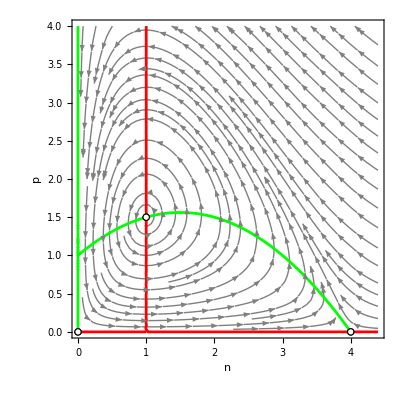

```mathematica
Show[
PlotEcoPhasePlane[{n,0,4.4},{p,0,4}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
```

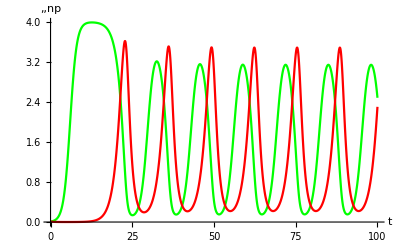

```mathematica
sol=EcoSim[{n->0.01,p->0.01},100];
PlotDynamics[sol]
```

Let's find the limit cycle and add it to the phase plane.

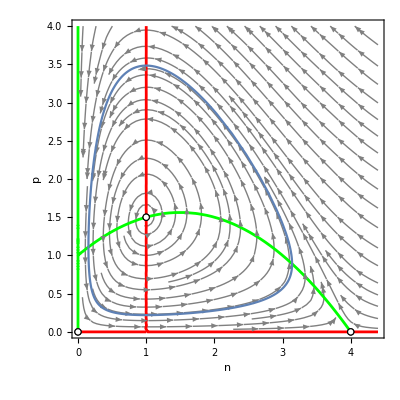

```mathematica
lc=FindEcoCycle[FinalSlice[sol]];
Show[
PlotEcoPhasePlane[{n,0,4.4},{p,0,4}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]],
RuleListPlot[lc]
]
```

### References

Related Tutorials

ExampleModels